## Import Raw Data

```mathematica
rawCoordinates = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

## List of distances

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
flatPairNames=Flatten[PairNames];
```

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

```mathematica
flatPairNames[[1]]
```

1and2.mx

```mathematica
currentPairData=Import[FileNameJoin[{dataDirectory,flatPairNames[[1]]}]];
```

Make a list for each pair that has True or False if they are associated for each time step.
- Split at each point where the larger threshold is crossed
- lists that contain values below the smaller threshold are considered connected
- Join back and make clusters, omitting missing sheep

```mathematica
testSplit=Split[currentPairData,( #1<50&&#2<50||#1>50&&#2>50||#1===Indeterminate&&#2===Indeterminate&)]
```

{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,286,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},894,{Indeterminate}}
 |  |  |  |

```mathematica
testListResult=MemberQ[#,_?(Function[x,x<30])]&/@testSplit
```

```mathematica
testFinalAssociation=Catenate[MapIndexed[Table[testListResult[[First[#2]]],Length[#1]]&,testSplit]]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,208135,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

```mathematica
determineConnections[pair_,{r1_,r2_}]:=
Module[{split,testList,final},
split=Split[pair,( #1<r2&&#2<r2||#1>r2&&#2>r2||#1===Indeterminate&&#2===Indeterminate&)];
testList=MemberQ[#,_?(Function[x,x<r1])]&/@split;
final =Catenate[MapIndexed[Table[testList[[First[#2]]],Length[#1]]&,split]]
]
```

```mathematica
determineConnections[currentPairData,{30,50}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,210299,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

```mathematica
<|1->{1->2}
```

## Run it on everything

```mathematica
allPairData=Map[Import[FileNameJoin[{dataDirectory,#}]]&,PairNames,{2}];
```

```mathematica
MostPairData=allPairData[[All,All,700;;770]]
```

{1}
 |  |  |  |

```mathematica
testcons=Transpose[Catenate[Map[determineConnections[#,{30,50}]&,MostPairData,{2}]]];
```

```mathematica
Dimensions[%159]
```

{71,1275}

```mathematica
Binomial[51,2]
```

1275

```mathematica
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,PairNames,{2}]];
```

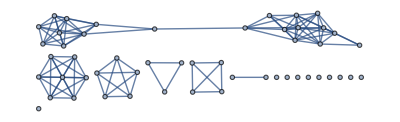
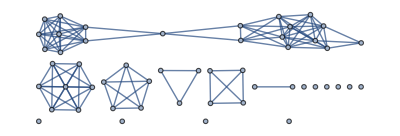
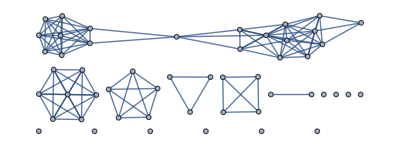
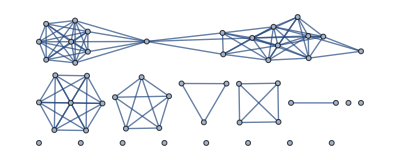
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[Range[51],Pick[allEdges,#]]&/@testcons[[;;5]]
```

```mathematica
ConnectedComponents[Graph[Range[51],Pick[allEdges,#]]]&/@testcons;
```

```mathematica
symmetricalStickyDBSCAN[data_,{r1_,r2_},{tmin_:1,tmax_:210351}]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,PairNames,{2}]];
ConnectedComponents[Graph[Range[51],Pick[allEdges,#]]]&/@cons]
```

```mathematica
DBSCAN30Sticky50LonelySheep=symmetricalStickyDBSCAN[allPairData,{30,50},{1,210351}];
```

## Plot Results

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],2]]]]/100}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Large],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep];
```

```mathematica
coloredGraph[graph30Sticky50,10]
```

```mathematica
DBSCAN30Sticky50LonelySheep[[;;2]]
```

{{{38,5,8,17,21,22,33,35,40,44,48},{15},{16},{25},{7},{28},{34},{29},{39},{20},{37},{50},{9},{43},{46},{32},{41},{4},{51},{13},{19},{27},{30},{3},{42},{45},{11},{14},{26},{47},{10},{12},{49},{18},{24},{36},{31},{1},{2},{6},{23}},{{38,2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,39,40,41,42,44,45,46,47,48,51},{15},{28},{50},{43},{32},{13},{30},{49},{1},{6}}}